```mathematica
(* This notebook provides methods for computing the zero forcing number, skew forcing number, and psd forcing number with additional functions *)

Clear[ZeroForcingOneStep,SkewForcingNumber];

ZeroForcingOneStep[A_,z_]:=
Module[{y,zz,zzz},
(y=Boole[#==-1]&/@((DiagonalMatrix[Total[A]]-A).z);
zz=z-A.y;
zzz=Boole[#>=1]&/@zz;
Return[zzz];
);
];
(* This function is a subroutine tht  computing one step of the zero forcing process. It takes an adjacency matrix A an indicator vector z;
The indicator vector z is of the vertices which are ****NOT**** colored 
and returns a 0-1 corresponding to the vertices not colored after one forcing step. *)
(* Adjacency matrix A; A ***can*** be a multigraph adjaceny matrix.
black/white vector z. 1 = white, 0 = black *)

ZeroForcingSteps[A_,z_,d_:1]:=
Module[{zk,z1,z2},
(If[Length[z]!=Length[A],
zk=Table[Boole[!MemberQ[z,ik]],{ik,1,Length[A]}];,
zk=z;
];
z1=zk;
z2=ZeroForcingOneStep[A,z1];
While[z1≠z2,
z1=z2;
z2=ZeroForcingOneStep[A,z1];
];
Return[Total[z1]==0];
);
];
(* This function reiterates the previous subroutine to compute the closure of the zero initially colored set z. As before the 
black, white vector z is 1 = white, 0 = black *)


ZeroForcingQ[A_,z_]:=
Module[{zk,z1,z2},
(If[Length[z]!=Length[A],
zk=Table[Boole[!MemberQ[z,ik]],{ik,1,Length[A]}];,
zk=z;
];
z1=zk;
z2=ZeroForcingOneStep[A,z1];
While[z1≠z2,
z1=z2;
z2=ZeroForcingOneStep[A,z1];
];
Return[Total[z1]==0];
);
];
(* This function takes an adjacency matrix A an indicator vector z;
The indicator vector is of the vertices which are NOT colored 
and returns True or False depending upon whether or not the initial vector z eventually colors the whole graph *)

FortQ[A_,z_]:=
Module[{zk,z1,z2},
(If[Length[z]!=Length[A],
zk=Table[Boole[!MemberQ[z,ik]],{ik,1,Length[A]}];,
zk=z;
];
z1=zk;
z2=ZeroForcingOneStep[A,1-z1];
Return[1-z1==z2];
);
];
(* This function takes an adjacency matrix A an indicator vector z;
The indicator vector is of the vertices which are NOT colored 
and returns True or False depending upon whether or not the initial vector z eventually colors the whole graph *)

ErrorPolynomial[GG_,S_]:=(
Clear[x];
Module[{q,colored,Alists,G,n,uncolored,qold,qsort,ucan,forcing,polys,active},
If[MatrixQ[GG],G=AdjacencyGraph[GG];,G=GG;];
n=VertexCount[G];
q=ConstantArray[0,n];
q[[S]]=1;
qold=q+1;
uncolored=Select[Range[n],Total[CoefficientList[q[[#]],x]]==0&];
colored=Complement[Range[n],uncolored];
While[Length[uncolored]>0&&Not[q===qold],qold=q;
Alists=AdjacencyList[G,#]&/@Range[n];
active=Select[colored,Length[Intersection[Alists[[#]],uncolored]]==1&];
ucan=Select[uncolored,Length[Intersection[Alists[[#]],active]]>0&];
If[Length[ucan]>0,polys=x*Total[q[[Alists[[#]]]]]+x*q[[#]]&/@Range[n];
qsort=SortBy[colored,Reverse[CoefficientList[polys[[#]],x]]&];
qsort=Join[qsort,uncolored];
For[i=1,i≤Length[ucan],i++,forcing=Intersection[Alists[[ucan[[i]]]],active][[1]];
q[[ucan[[i]]]]=polys[[forcing]];];];
uncolored=Select[Range[n],Total[CoefficientList[q[[#]],x]]==0&];
colored=Complement[Range[n],uncolored];];
Return[Expand[q]];])
(* Computes the error poylnomial on graph GG with zero forcing set SS. GG an be a graph object or an adjaceny matrix. If SS is not a zero forcing set, then all unforced vertices will return a polynomial of 0. For more information see:

Kenter,F.H.,& Lin,J.C.H.(2019)." On the error of a priori sampling:zero forcing sets and propagation time." Linear Algebra and its Applications,576,124-141.
*)

Clear[ErrorVPolynomial];
ErrorVPolynomial[GG_,S_]:=(Clear[x];
Module[{q,colored,Alists,G,n,uncolored,qold,qsort,ucan,forcing,polys,active},
If[MatrixQ[GG],G=AdjacencyGraph[GG],G=GG];
n=VertexCount[G];
q=ConstantArray[0,n];
q[[S]]=Array[Subscript[ϵ, #]&,Length[S]];
qold=q+1;
uncolored=Select[Range[n],Total[CoefficientList[q[[#]],x]]==0&];
colored=Complement[Range[n],uncolored];
While[Length[uncolored]>0&&Not[q===qold],qold=q;
Alists=AdjacencyList[G,#]&/@Range[n];
active=Select[colored,Length[Intersection[Alists[[#]],uncolored]]==1&];
ucan=Select[uncolored,Length[Intersection[Alists[[#]],active]]>0&];
If[Length[ucan]>0,
polys=x*Total[q[[Alists[[#]]]]]+x*q[[#]]&/@Range[n];
qsort=SortBy[colored,Reverse[CoefficientList[polys[[#]],x]]&];
qsort=Join[qsort,uncolored];
For[i=1,i≤Length[ucan],i++,forcing=Intersection[Alists[[ucan[[i]]]],active][[1]];
q[[ucan[[i]]]]=polys[[forcing]];];];
uncolored=Select[Range[n],Total[CoefficientList[q[[#]],x]]==0&];
colored=Complement[Range[n],uncolored];];
varq=∑_(i=1)^Length[S] Coefficient[q,Subscript[ϵ, i]]^2;
Return[Expand[varq]];])
(* Computes the variance poylnomial on graph GG with zero forcing set SS. GG an be a graph object or an adjaceny matrix. If SS is not a zero forcing set, then all unforced vertices will return a polynomial of 0. For more information see:

Kenter,F.H.,& Lin,J.C.H.(2019)." On the error of a priori sampling:zero forcing sets and propagation time." Linear Algebra and its Applications,576,124-141.
*)



Clear[ZeroForcingNumber];
ZeroForcingNumber[A_,WAVEFRONT_:True, TRACKING_:True,UB_:0]:=
(* WAVEFONT doesn't do anything, ignore it *)
Module[{GA,maxdeg,ub,result,or,subsets,i},
(* A is an Adjacency Matrix *)
(If[GraphQ[A],Return[ZeroForcingNumber[Normal[AdjacencyMatrix[A]],WAVEFRONT, TRACKING,UB]]];
(* If you acdientally input a graph, this will fix it *)
GA=AdjacencyGraph[A];
If[GraphDiameter[GA]==VertexCount[GA]-1&&SimpleGraphQ[GA],Return[{1,{1}}]];
If[EdgeCount[GA]==0,Return[{VertexCount[GA],Range[VertexCount[GA]]}]];
(* If A corresponds to a path, return 1, if it is empty, return n *)
maxdeg=Max[A.(1&/@ A)];
If[SimpleGraphQ[GA],ub=Ceiling[(maxdeg-1)/maxdeg*Length[A]];,ub=Length[A]];  (* A-C-D-Pepper Bound *)
If[UB≠0,ub=Min[ub,UB];];
results={};
subsets=Table[Boole[!MemberQ[#,ub]],{i,1,Length[A]}]&/@Subsets[Range[Length[A]],{Length[A]-ub}];
For[i=Length[A]-ub,i<Length[A],i++,
subsets=Table[Boole[!MemberQ[#,i]],{i,1,Length[A]}]&/@Subsets[Range[Length[A]],{Length[A]-i}];
or=result;
result=Select[subsets,ZeroForcingQ[A,#]&];
If[TRACKING&&result≠{},
subsets=DeleteDuplicates[Table[subsets[result[[i]],Length[A]-i-1],{i,1,Length[result]}]];
];


If[Length[result]==0, Return[{Length[A]-i+1,Flatten[Position[or[[1]],0]]}];i=0;];
];
If[Total[Total[A]]==0,Return[{0,{0}}],Return[{1,{0}}];];
);
];

(* There are the analogous functions for KForcing and Skew Forcing and PSD Forcing *)
KForcingOneStep[A_,el_,k_:1]:=
Module[{y,zz,zzz},
(y=Sign[Boole[(#<=-1)&&(#≥-k)]&/@((DiagonalMatrix[Total[A]]-A).el)];
zzz=1-Sign[A.y+(1-el)];
Return[zzz];
)
];
(* This function takes an adjacency matrix A an indicator vector z;
The indicator vector is of the vertices which are NOT colored 
and returns a 0-1 corresponding to the vertices not colored after one forcing step. *)

SkewForcingOneStep[A_,z_]:=
Module[{y,zz,zzz},
(y=Boole[#==-1]&/@((-A).z);
zz=z-A.y;
zzz=Boole[#>=1]&/@zz;
Return[zzz];
);
];
(* This function takes an adjacency matrix A an indicator vector z;
The indicator vector is of the vertices which are NOT colored 
and returns a 0-1 corresponding to the vertices not colored after one skew forcing step. *)

PSDForcingOneStep[A_,z_,G_]:=
Module[{y,zz,zzz,precolored},
(colored=Flatten[Position[z,0]];
comps=ConnectedComponents[VertexDelete [G,colored]];
y=Boole[#==-1]&/@((DiagonalMatrix[Total[A]]-A).z);
zz=z-A.y;
zzz=Boole[#>=1]&/@zz;

compboole=Table[Boole[MemberQ[#,i]],{i,1,Length[A]}]&/@comps;
neighborhoods=A[[Flatten[Position[z,0]]]];

intersects=Outer[Times,compboole,neighborhoods,1,1];
If[Length[intersects]≥1,intersects=Flatten[intersects,{1,2}],intersects={Table[0,{i,1,Length[A]}]}];
zzz=zzz-Sign[Total[Select[intersects,Total[#]<=1&]]];
zzz=Max[#,0]&/@zzz;
Return[zzz];
);
];

Clear[SkewForcingNumber];
SkewForcingNumber[A_,WAVEFRONT_:True, TRACKING_:True,UB_:0]:=
(* WAVEFONT doesn't do anything, ignore it *)
Module[{GA,maxdeg,ub,result,or,subsets,i},
(* A is an Adjacency Matrix *)
(If[GraphQ[A],Return[SkewForcingNumber[Normal[AdjacencyMatrix[A]],WAVEFRONT, TRACKING,UB]]];
(* If you acdientally input a graph, this will fix it *)
GA=AdjacencyGraph[A];
If[EdgeCount[GA]==0,Return[{VertexCount[GA],Range[VertexCount[GA]]}]];
(* If A corresponds to a path, return 1, if it is empty, return n *)
If[SkewForcingQ[A,{}],Return[{0,0}]];
maxdeg=Max[A.(1&/@ A)];
ub=Ceiling[(maxdeg-1)/maxdeg*Length[A]];  (* A-C-D-Pepper Bound *)
If[UB≠0,ub=Min[ub,UB];];
results={};
subsets=Table[Boole[!MemberQ[#,ub]],{i,1,Length[A]}]&/@Subsets[Range[Length[A]],{Length[A]-ub}];
For[i=Length[A]-ub,i<Length[A]+1,i++,
subsets=Table[Boole[!MemberQ[#,i]],{i,1,Length[A]}]&/@Subsets[Range[Length[A]],{Length[A]-i}];
or=result;
result=Select[subsets,SkewForcingQ[A,#]&];

If[TRACKING&&result≠{},
subsets=DeleteDuplicates[Table[subsets[result[[i]],Length[A]-i-1],{i,1,Length[result]}]];
];


If[Length[result]==0, Return[{Length[A]-i+1,Flatten[Position[or[[1]],0]]}];i=0;];
];
If[Total[Total[A]]==0,Return[{0,{0}}],Return[{1,{0}}];];
);
];

Clear[PSDForcingNumber];
PSDForcingNumber[A_,WAVEFRONT_:True, TRACKING_:True,UB_:0]:=
(* WAVEFONT doesn't do anything, ignore it *)
Module[{GA,maxdeg,ub,result,results,or,subsets,i,},
(* A is an Adjacency Matrix *)
(If[GraphQ[A],Return[PSDForcingNumber[Normal[AdjacencyMatrix[A]],WAVEFRONT, TRACKING,UB]]];
(* If you acdientally input a graph, this will fix it *)
GA=AdjacencyGraph[A];
maxdeg=Max[A.(1&/@ A)];
ub=Ceiling[(maxdeg-1)/maxdeg*Length[A]];  (* ACDPepper Bound *)
(* If[WAVEFRONT,ub=Total[1-WavefrontZF[A]];]; *)
If[UB≠0,ub=Min[ub,UB];];
results={};
subsets=Table[Boole[!MemberQ[#,ub]],{i,1,Length[A]}]&/@Subsets[Range[Length[A]],{Length[A]-ub}];
For[i=Length[A]-ub,i<Length[A],i++,
subsets=Table[Boole[!MemberQ[#,i]],{i,1,Length[A]}]&/@Subsets[Range[Length[A]],{Length[A]-i}];
or=result;
result=Select[subsets,PSDForcingQ[A,#,GA]&];
If[TRACKING&&result≠{},
subsets=DeleteDuplicates[Table[subsets[result[[i]],Length[A]-i-1],{i,1,Length[result]}]];
];
If[Length[result]==0, Return[{Length[A]-i+1,Flatten[Position[or[[1]],0]]}];i=0;];
];
If[Total[Total[A]]==0,Return[0],Return[1];];
);
];


KForcingQ[A_,z_,k_:1]:=
(If[Length[z]!=Length[A],
zk=Table[Boole[!MemberQ[z,ik]],{ik,1,Length[A]}];,
zk=z;
];
z1=zk;
z2=KForcingOneStep[A,z1,k];
While[z1≠z2,
z1=z2;
z2=KForcingOneStep[A,z1,k];
];
Return[Total[z1]==0];
)
(* This function takes an adjacency matrix A an indicator vector z;
The indicator vector is of the vertices which are NOT colored 
and returns True or False depending upon whether or not the initial vector z eventually colors the whole graph *)

SkewForcingQ[A_,z_]:=
(If[Length[z]!=Length[A],
zk=Table[Boole[!MemberQ[z,ik]],{ik,1,Length[A]}];,
zk=z;
];
z1=zk;
z2=SkewForcingOneStep[A,z1];
While[z1≠z2,
z1=z2;
z2=SkewForcingOneStep[A,z1];
];
Return[Total[z1]==0];
)
(* This function takes an adjacency matrix A an indicator vector z;
The indicator vector is of the vertices which are NOT colored 
and returns True or False depending upon whether or not the initial vector z eventually colors the whole graph *)

PSDForcingQ[A_,z_,G_]:=
(If[Length[z]!=Length[A],
zk=Table[Boole[!MemberQ[z,ik]],{ik,1,Length[A]}];,
zk=z;
];
z1=zk;
z2=PSDForcingOneStep[A,z1,G];
While[z1≠z2,
z1=z2;
z2=PSDForcingOneStep[A,z1,G];
];
Return[Total[z1]==0];
)

Clear[KForcingNumber];
KForcingNumber[A_,k_:1,WAVEFRONT_:False, TRACKING_:True,UB_:0]:=
(* A is an Adjacency Matrix *)
(* I beleive this code fails for empty graphs *)
(If[GraphQ[A],Return[KForcingNumber[Normal[AdjacencyMatrix[A]],k,WAVEFRONT, TRACKING,UB]]];
maxdeg=Max[A.(1&/@ A)];
If[maxdeg==0,Return[Length[A]]];
ub=Ceiling[(maxdeg-1)/maxdeg*Length[A]]; 
If[WAVEFRONT,ub=Total[1-WavefrontZFk[A,k]];];
If[UB≠0,ub=Min[ub,UB];];
results={};
subsets=Table[Boole[!MemberQ[#,ub]],{i,1,Length[A]}]&/@Subsets[Range[Length[A]],{Length[A]-ub}];
(* ub may be off *)
For[i=Length[A]-ub,i<Length[A],i++,
subsets=Table[Boole[!MemberQ[#,i]],{i,1,Length[A]}]&/@Subsets[Range[Length[A]],{Length[A]-i}];
or=result;
result=Select[subsets,KForcingQ[A,#,k]&];
If[TRACKING&&result≠{},
subsets=DeleteDuplicates[Table[subsets[result[[i]],Length[A]-i-1],{i,1,Length[result]}]];
];
If[Length[result]==0,Return[Length[A]-i+1];i=0;];
];
If[Total[Total[A]]==0,Return[0],Return[1];];
);
```

```mathematica
(* This function simple gives the atlas graph "GX" from the "Atlas of Graphs" where "X" is an integer between 0 and 1254. *)

atlas[n_]:=
If[n<=1254&&n>0&&IntegerQ[n],
ImportString[{"?", "@", "A?", "A_", "B?", "BG", "Bo", "Bw", "C?", "C@", "CB", "C`", "CJ", "CF", "Ck", "CN", "Cl", "C|", "C~", "D??", "D?C", "Dg?", "DOC", "Dw?", "DBC", "D@c", "DgC", "DJC", "Dl?", "D?{", "DBc", "Dh_", "DwC", "D|?", "D@{", "Dx_", "DJc", "DbW", "Dhc", "Des", "DjW", "Db[", "D`{", "Dlc", "D]o", "DJ{", "DF{", "Djs", "D]w", "Df{", "Dl{", "Dn{", "D~{", "E???", "E??G", "EC?G", "EI??", "EJ??", "ECa?", "E?EG", "E?D_", "EK?G", "ECaG", "EC_W", "E?Bo", "EBc?", "EY?O", "EJA?", "EKa?", "EGEG", "EQ_O", "ECaW", "EBCW", "E@cW", "EJc?", "EHs?", "Ehc?", "E?Bw", "EhP?", "EsCO", "EiGO", "EBe?", "Ej?G", "E`EG", "ECd_", "EK_W", "ECeW", "EB{?", "EJw?", "EOkW", "Elc?", "ErW?", "E?Fw", "EC{O", "E@dW", "EG}?", "E]a?", "EYWO", "E]_O", "EQKo", "EsCW", "EKaW", "EJe?", "EBy?", "Ehd?", "EhEG", "EJaG", "E~A?", "EzW?", "Ejs?", "Ev@_", "EB{G", "EhX_", "E^_O", "EJwG", "E`Xg", "E~?G", "EtaG", "Eht?", "EtoO", "EB}?", "EXSg", "Eld?", "EJy?", "Exd?", "EYOw", "ERUO", "EZEG", "ElEG", "EheO", "E{CW", "E~@_", "El{?", "E~a?", "E~_O", "EzW_", "Ejt?", "EjsG", "Ez`_", "Eju?", "Ev`_", "EXSw", "E~AG", "Er`o", "EB}G", "Exe_", "E?~o", "EhMg", "EyUG", "Ele_", "EJyG", "EhdW", "EhNG", "Ehf_", "EhUg", "En{?", "E~H_", "E~`_", "El{G", "EZSw", "E~@g", "E?~w", "E|e_", "EyuG", "EyVG", "E~aG", "ElfO", "E^eG", "E^MG", "Exf_", "EO~o", "Ehew", "Elf_", "ElMg", "EtTg", "ElUg", "E~{?", "En{G", "En}?", "E_~w", "EjtW", "E^mG", "E^Mg", "EjvG", "Elfo", "Exv_", "ErXw", "Ehfw", "EzNG", "E^NG", "EyUw", "E~|?", "E~Xo", "En}G", "E~wW", "EyVw", "ER~g", "E}^G", "Ep~o", "El^g", "E~{W", "E~z_", "Ep~w", "E~^G", "EznW", "E~~G", "E~nW", "Ez~w", "E~~w", "F????", "F???G", "FH???", "F??K?", "FOg??", "F_AC?", "F??KG", "FH??G", "FA_?G", "FG?`G", "FGOg?", "FgP??", "Fg?`?", "FhC??", "FOg?G", "F_IC?", "FA?KG", "FC_`?", "FH?K?", "Feo??", "F@G`G", "FOgK?", "Fg?`G", "FMo??", "Fhc??", "F?Bw?", "Fh@A?", "FHP@?", "FHDA?", "FHCG_", "FGC`G", "F_CKG", "FC_`G", "F@O_g", "FiO?G", "Fk_?G", "FK_`?", "FhC?G", "FH?KG", "F`?GW", "FG@bG", "FjW??", "FMs??", "F@Gh_", "Fgog?", "FWJG?", "FHG`G", "FJO`?", "F_@Ig", "FEPAG", "FDg`?", "FJO_G", "FH?gg", "FIO`G", "FDgG_", "Feo?G", "FBO`G", "FGOgg", "FaOGg", "FhEG?", "FCc`G", "F??Fw", "FhG`?", "FiO`?", "FiOG_", "FiO_G", "F`G`G", "FIo`?", "Fx_?G", "Fk_`?", "FaOH_", "FEW`?", "FLg?G", "FK_`G", "FgC`G", "Fk_G_", "FaO`G", "FhCK?", "Fh?GW", "F`__g", "Fhc?G", "Fj[??", "FWJg?", "Fjs??", "FwJG?", "FTg`?", "FjW@?", "Fb[?_", "FDk`?", "FeoG_", "Fes?G", "FHGh_", "Fxc_?", "FBGh_", "FZWC?", "FWJW?", "FxcO?", "Fxd??", "F@KqO", "F[JG?", "FIT@G", "FhoW?", "FHHGg", "FHOgg", "FIS`G", "FsaC_", "FItA?", "F?Bcw", "FkoK?", "FhG`G", "FMpA?", "FhoI?", "FhoGO", "FHAgg", "Fmo?G", "FiG`G", "FbW`?", "FiO`G", "FMoG_", "Fg?hg", "Fko`?", "FMs?G", "Fpq?_", "FMoa?", "Fpq?G", "Fpa?g", "F`{?G", "FhoG_", "FhD@G", "FhoGG", "FIo`G", "Fh_gG", "FpQO_", "FXAGg", "Fk_`G", "FMo`?", "Fgog_", "Feo`?", "FFw?G", "FK_h_", "FIc`G", "FMo@G", "FPq?g", "FKc`G", "FhCKG", "F`o_g", "Fgxg?", "Fwqg?", "FetA?", "FHXgG", "FixG?", "FTaCg", "FwagG", "FjKo?", "FTAKg", "Fg\\\\o?", "FG\\\\oO", "Fms_?", "FK\\\\o?", "FTg`G", "FPIgg", "F?~o?", "FHPgg", "FDgh_", "FFwg?", "FDk`G", "FbAbG", "FTgGg", "FhNG?", "FgAlO", "FmpA?", "FupA?", "FexA?", "FMtA?", "F\\\\CoG", "FE|A?", "F[EoG", "FjKGO", "Fms?G", "F`?Fw", "FH?NW", "Fh?Dw", "Fepa?", "Flg`?", "FXAgg", "FhDb?", "FmW`?", "FFwG_", "FgxG_", "FxUA?", "FeoJ?", "Fewa?", "FxSI?", "FxSQ?", "FEtB?", "FxaGG", "FFwH?", "Fhoh?", "Fh?N_", "Fmo`?", "Fh?JW", "Fpa_g", "FFw`?", "FjCHO", "F`DbG", "FhogG", "FMs`?", "FFwc?", "Ffw?G", "F`_pg", "FLg`G", "FwaK_", "FxOY?", "FxSAG", "FhFE?", "FK{@G", "FsNA?", "F_{p?", "FhT@G", "FhDIO", "F_{Og", "FSYK_", "FFwGG", "Fgogg", "FxOWO", "FHt@G", "FHFEG", "F_sPg", "FhFK?", "FhMK?", "FxU?G", "FHhGg", "FLJK?", "FFw_G", "F_{PG", "F`EBW", "Fh_gg", "FhEJ?", "FMo`G", "FhEIG", "FhEK_", "F`ooo", "Feo`G", "Fn{??", "F~H_?", "F~`_?", "Fl{G?", "FZSw?", "F~@g?", "F?~w?", "F|e_?", "FyuG?", "FyVG?", "F~aG?", "FlfO?", "F^eG?", "F^MG?", "Fxf_?", "FO~o?", "Fhew?", "Flf_?", "FlMg?", "FtTg?", "FlUg?", "F~aC?", "F~a@?", "F~_Q?", "FzW`?", "FzWa?", "FjtA?", "Fjt?O", "Fz`a?", "FjsGO", "FjsG_", "Fz`c?", "FjuA?", "FXSx?", "Fv`c?", "F~a?G", "Fju?O", "FjsH?", "FXSwG", "F~_?g", "FjuC?", "FlkG_", "Fz`_G", "FXSwO", "F~@_O", "Fju@?", "Fv`_G", "Fv@h?", "Fr`s?", "F~AGG", "Fl{?G", "FB}GO", "Fxec?", "FB}G_", "FzW_G", "F?~oO", "FhMh?", "FjsAG", "FB}H?", "FB}K?", "FyQAg", "Flec?", "FJyGO", "FjsGG", "FhMgO", "FhMgG", "FyaAg", "Fxea?", "Fxe_O", "FJyH?", "Fle__", "Fle`?", "Fz@cO", "F?~q?", "Fju?G", "FhMi?", "FhMk?", "FhMg_", "FyIAg", "FhdW_", "Flea?", "FhNGO", "Fv@cO", "Fhfa?", "FJyK?", "FHS|?", "Fhfc?", "FhdWG", "Fle_O", "FyAIg", "FhUgG", "FhdY?", "FJyG_", "F~AGO", "Fhd[?", "Fhf_O", "FhNK?", "Fr@sO", "FhUk?", "FGEFw", "FxS`G", "FB{KG", "FByGo", "FXQgg", "FBqgW", "FxCX_", "FXJGg", "FjSKG", "FhdM?", "Fht@G", "FxSOg", "FxaGg", "FhdU?", "Fp`gg", "FhYGo", "Fmo`G", "FBZEG", "Fpq_g", "FFw`G", "FpUK_", "FhEM_", "FlO[O", "Fhogg", "FgqPg", "FMs`G", "FhEMG", "FlgGg", "FhMIG", "FhcYG", "FhELO", "FKdbG", "F~{??", "Fn{G?", "Fn}??", "F_~w?", "FjtW?", "F^mG?", "FjvG?", "F^Mg?", "Fxv_?", "Flfo?", "FrXw?", "Fhfw?", "FzNG?", "F{\\\\o?", "FyUw?", "F~H`?", "F~Ha?", "F~`a?", "F~`c?", "F~`__", "Fl{GO", "FZSw_", "F~@h?", "FZSx?", "FxqgG", "F~`_G", "FZSwO", "F~@gG", "Fn{?G", "F?~wG", "F|ec?", "F|e`?", "F?~y?", "F|e__", "FyuK?", "FyVI?", "F~aK?", "FlfO_", "F|e_G", "F^eG_", "FyVK?", "FPzp?", "F~@`O", "Fxf`?", "FyVGG", "F|e_O", "F^MG_", "F~aH?", "FO~oG", "F^eH?", "FPzs?", "FlfQ?", "F^MGO", "F~@cO", "Fxf_G", "FyuGG", "FO~s?", "FyVH?", "FlMh?", "FhewG", "Flfc?", "F~aGG", "Fl{?W", "F^eI?", "FlfOO", "FhewO", "FlfP?", "Fhe{?", "FlMgG", "Flfa?", "Fxf__", "FJS|?", "FhDjO", "FlMk?", "Flf__", "Flf`?", "F~@_W", "F^MI?", "F^MGG", "FO~q?", "Fhey?", "FlMi?", "Flf_O", "FtTgO", "FlUk?", "FjrE?", "FXJgg", "F]rE?", "FGENw", "F`EFw", "FxUb?", "FxUd?", "FGeJw", "FxKiO", "Fmqd?", "FXJHg", "FxVD?", "FxeHO", "FF{`G", "FzSIG", "FHENW", "F`EVW", "FhayG", "F]mCG", "F]uCG", "F`MFW", "FMpbG", "Fowt_", "FOx{_", "FLsYG", "Fgkx_", "FxSIW", "FhFIg", "Fpq`g", "FhdYG", "Fh]IG", "FxSqO", "FxckG", "FsdoW", "FhNHG", "FF}@G", "FhcWw", "FHVf?", "FhNHO", "FdZKO", "FMowo", "Fhf_g", "Fhowg", "FhMJG", "FheoW", "FheL_", "FhEKw", "FhFMO", "FxEKW", "FhEMg", "FXVEG", "FhdQW", "FhUkG", "FMjDO", "FhEJW", "F]MIO", "F`NBW", "Ffw`G", "Fms`G", "FMohg", "FhMMG", "FlBHo", "FhUk_", "F~|??", "F~Xo?", "Fn}G?", "F~wW?", "FyVw?", "F@Tjw", "F}BBg", "Fp~o?", "Fl^g?", "Fn{GO", "Fn{OO", "Fn{_O", "Fn{`?", "Fn{c?", "F~{?G", "F_~wO", "FjtY?", "FjtWO", "F_~y?", "F^mH?", "FjtWG", "F^Mh?", "FjvI?", "F^Mg_", "FjvGO", "F@`zw", "Flfs?", "F^Mk?", "Fxva?", "FjvGG", "Fjt[?", "FrXx?", "FjvG_", "Fxv`?", "F^MgG", "FlfoG", "FrXwG", "Fn{GG", "Flfq?", "Fxv_O", "Fxv_G", "FrXwO", "F^mI?", "Fn{@G", "FhfwG", "FzNI?", "Fhfy?", "FjvH?", "F^Mi?", "F?\\\\vg", "FyUy?", "FzNGG", "FzNG_", "FlfoO", "Fxv__", "F^NI?", "FyUx?", "FrX{?", "F?\\\\~_", "F?B~w", "FzTb?", "FjtQO", "FF[Kw", "FxMhO", "F|eK_", "Fz[`G", "FXYwg", "FhmhO", "Fxef?", "F@FnW", "F?F~o", "FGM]w", "FxkkG", "FxkKW", "Fp\\\\j?", "FhNhO", "FxeLO", "FjsYG", "FN{`G", "F@U}o", "Fhxgg", "FF|b?", "F`ENw", "FmpbG", "Fl{GW", "Fxecg", "FxeKo", "FxecW", "FleL_", "FhA{w", "FzKWg", "Ff[sO", "FrD{_", "FVrEG", "Fh]Ho", "FhFWw", "Fhhwg", "Fl|?W", "Fnw`G", "FcBzo", "FxT`o", "FxJ_w", "FhtOw", "FheTg", "FhFIw", "FhNJG", "FlkqO", "FhFJW", "FKL\\\\W", "FpNDW", "Fhctg", "FFx]?", "FBUlW", "F}?^O", "Fxqgg", "FpTz?", "F?]~_", "FxeHo", "F}oXO", "Fhff?", "Fm{`G", "FheyG", "Fhqwg", "FllGW", "Fhbwo", "FMtbG", "FNohg", "Flg[g", "FsW|_", "Fhe}?", "FKhZg", "FhuoW", "F`~PG", "FMshg", "FfxcG", "FDpjg", "FllIG", "Fhqhg", "FlkYG", "FhsZG", "FhNHo", "FlUj?", "FK`zo", "FlhWo", "FBjN_", "FLNMO", "Frq_w", "F{cZG", "F~{W?", "F}BFg", "Fy^w?", "F~^G?", "FznW?", "F~|A?", "F~{OO", "F~Xq?", "F~Xo_", "Fn}GO", "Fn}I?", "F~Xs?", "Fn}K?", "Fn}H?", "F~wY?", "F~wWO", "F~{AG", "FyVy?", "FlNwG", "F}RBg", "FlNw_", "F~XoO", "FyVx?", "F}bBg", "FR~g_", "FR~k?", "Fn}GG", "Fl^gG", "Fp~oO", "Fp~s?", "F}BJg", "Fp~o_", "Fl^k?", "F~wWG", "FFC^w", "Fh|JO", "FD^Ww", "F~MQ_", "F~ZC_", "FhxxG", "Ff{Wg", "FnzE?", "F~gj?", "Fl{go", "FnzB?", "F~ghO", "F{e[o", "F~q`G", "Fl}SO", "FlzM?", "Fnye?", "FlkXo", "FD^[g", "Fl~E?", "Fn|?W", "FnwWo", "Flu]?", "Fnz@O", "FlxiG", "F}lQO", "F|sk_", "Fxr`g", "FnwpO", "Fw\\\\x_", "F}{Gg", "F~CRW", "Fn}CG", "Fl|c_", "FhdYw", "FBY|o", "FhffG", "F`FNw", "FhfyG", "Fl|GW", "FwVy_", "FB`~W", "F@Vng", "F{XrO", "FllWo", "FyUyG", "Fl|EG", "FfxbO", "FlZZ?", "FlZYO", "FlZ]?", "FllHo", "FBj]g", "FKNJw", "FDXmw", "Fhc^o", "FvXqO", "FyUy_", "FL~@o", "FFj]_", "FC^bw", "FLrFo", "FBY^W", "FKYZw", "FC\\\\vW", "F?^vo", "Fl]Z?", "Fl]YG", "FPT}o", "FB]mg", "Fl]oW", "FXT[w", "FQ\\\\sw", "FQT|o", "FB]^G", "FHN]o", "FDh}o", "FJY[w", "FpLYw", "FFhuo", "FBjew", "FF|cg", "FFxso", "FJa^W", "FFhmo", "FL~Cg", "FKN^O", "FLUmW", "FLNMW", "Ffwhg", "Floxo", "FBfnO", "FEl~?", "F`urg", "FreRW", "FhENw", "FK|ko", "F@\\\\zw", "FBXzw", "F@\\\\|w", "F~{WO", "F}~I?", "Ftilg", "F@\\\\}w", "FC\\\\zw", "Fse|o", "F@\\\\~g", "FBX|w", "Fp~y?", "F~{WG", "FB^bw", "FBX~o", "FgB~w", "F~zD?", "Fn{[_", "Fn}S_", "Fn}SO", "FA]|w", "F~ySO", "F~|AG", "FBh|w", "F@]~g", "FBY|w", "F~{OW", "F@N~o", "FyVyG", "Fl}Ko", "FyVz?", "F~zCG", "FnZf?", "FN{hg", "FC\\\\~W", "FNxYo", "F}ys_", "F~ySG", "F~qk_", "F}mu?", "FPT}w", "FNlj_", "F@t~g", "FyuyO", "FtviG", "F~eqO", "F|VhG", "FFvHw", "FQT|w", "Fp~oW", "Fyu{O", "FfzM_", "FHN]w", "FyVwo", "F}th_", "F|bJW", "F@^vo", "FBY~o", "F~yOW", "FI]tw", "F^nKG", "Ftvh_", "Fljwo", "F`\\\\tw", "F`L~o", "Fhe|o", "Fxc{w", "Fnkpg", "Fhfww", "FnTNG", "F}qtO", "FN^Sg", "Fls{o", "Fh`}w", "F@vng", "FBfnW", "FxNgw", "FgF~o", "FreVW", "FHf^o", "F^TmO", "FltjG", "F@vvo", "FFh}o", "FHvTw", "FBnew", "FXU]w", "FhNvO", "FYU\\\\w", "Ffw}_", "F\\\\VMo", "FJe~O", "FIm~_", "Floxw", "Fb]lg", "FbY|o", "FzeRW", "Fz~w?", "F~~I?", "FB\\\\|w", "Fsmtw", "FB\\\\~W", "FK\\\\zw", "F~{Wo", "F~~B?", "F~{sO", "F}~KO", "F}vUO", "Fse~W", "Fsq|w", "Fyv{O", "Fyvz?", "Fse~o", "FFn]o", "F~{WW", "FztxG", "FD\\\\~W", "FK\\\\|w", "F@^~o", "F`\\\\|w", "FI]|w", "F~z_o", "FlnyG", "FJd~W", "FBx~g", "FB^ng", "F~v_W", "F^vm?", "FgF~w", "Fsfng", "FreVw", "FEynw", "FnzM_", "FC|vw", "FtrLw", "Fbk}w", "FBn^W", "FHn]w", "FFx{w", "FEyvw", "Feg~w", "F{e}o", "Ftj]o", "FFy}g", "Ffk}W", "FBnng", "FLp|w", "FIm~g", "F`]~g", "Fbh|w", "FFy}o", "FbY|w", "FJq|w", "F@~vg", "Ffw}o", "FBzvo", "FJfno", "FJnVW", "FLvbw", "FFzbw", "FzM]W", "FFzn_", "F~~w?", "Fz~y?", "Fz~{?", "F}vUg", "Fsn]w", "Fdn]w", "FF~]o", "Fl~yG", "FeN^w", "Fbn]w", "FR\\\\}w", "FFz]w", "FF~ww", "FF|{w", "F~nR_", "Fv|Xo", "F~{Ww", "Flknw", "Fek~w", "FEznw", "F~ENw", "FC~vw", "FJm}w", "FFy}w", "Ff}ew", "Fsnvo", "Few~w", "Fe]vw", "Ff]mw", "FU\\\\~W", "FBz~o", "FF~ew", "Ffw}w", "FJn^W", "Fs\\\\zw", "FtTnw", "Fs\\\\vw", "FLvng", "FF~n_", "Ff~`w", "Fhf~o", "F~~x?", "FEv~w", "Ftm}w", "FJ^~o", "FF~{w", "FEn~w", "Ftn]w", "FEz~w", "FeN~w", "Fe]~w", "Fum~W", "FE~vw", "Ffy}w", "Ff~ew", "F}vn_", "Ftvng", "Fs~vg", "F`~vw", "Ffx|w", "Ff~dw", "FFz~o", "F~~z?", "F~znO", "Fen~w", "Fe~vw", "Ff~xw", "Fd^~w", "FFz~w", "Fd~vw", "Ffznw", "FNz~o", "F~~}G", "F~~v_", "F|~lw", "F~^]w", "Fvx~w", "F~~]w", "F~^nw", "F~^~w", "F~~~w"}[[n+1]],"Graph6"],$Failed];
```

```mathematica
Clear[MultList];

(* This function Finds all "double-induced" *)
K23Q[G_]:=
(v23=Select[Tuples[{Subsets[VertexList[G],{2}],Subsets[VertexList[G],{3}]}],Intersection[#[[1]],#[[2]]]=={}&];
v23t=v23;

v23=Select[v23,IsomorphicGraphQ[Subgraph[G,Flatten[#]],CompleteGraph[{2,3}]]||IsomorphicGraphQ[Subgraph[G,Flatten[#]],EdgeAdd[CompleteGraph[{2,3}],1<->2]]&];
v23t2=v23;

DM=MatrixPower[AdjacencyMatrix[G],2];
v23=Select[v23,(1-IdentityMatrix[3])*DM[[#[[2]],#[[2]]]]==(1-IdentityMatrix[3])*ConstantArray[2,{3,3}]&];
(Subsets[#,{2}]&/@v23[[All,2]])
)

MultList[G_,q_,zfi_:0,pzfi_:0,tzfi_:0,tpsdi_:0,tpq_:False]:=
(
(* This function returns a list of ***potential*** multiplicty lists for the graph G with eqactly q eigenvalues. *)
(* G is a graph, 
q is the number of distinct eigenvalues, 
zfi, pzfi, tzfi, tpsdi are predefined bounds if you already know Z(G), Z+(G), Z^2(G), or Z+^2(G); the default value of 0 means that value will be calculated and overridden. tpq->True will print values. *)


(* We will optimize 1.x with constraints AM.x >= b *)


(* If you set "q" to "All" it will do all possible values *)

If[q==All,
zf=ZeroForcingNumber[G];
pd=PSDForcingNumber[G];
If[pd==1,pd={1,0}];
A=AdjacencyMatrix[G];
AM2=MatrixPower[A+2*IdentityMatrix[VertexCount[G]],2];
AM2=Sign[AM2-1]+1; (* This line isn't explictly necessary *)
zf2=ZeroForcingNumber[AM2];
If[pd2==1,pd2={1,0}];
pd2=PSDForcingNumber[AM2];

Return[
Array[
MultList[G,#,zf[[1]],pd[[1]],zf2[[1]],pd2[[1]]]&,Floor[VertexCount[G]/zf[[1]] ] ] ]];

(* Otherwise... *)
(* Initialize b and AM *)

b={};
AM={};

(* Add constraint that the sum of the multiplicities must be (at least) n *)

v=Array[1&,q];
b=Append[b,VertexCount[G]];
AM=Append[AM,v];

b=Join[b,Array[1&,q]];
AM=Join[AM,IdentityMatrix[q]];

(* Zero Forcing *)

(* For each q_i, i≠1,n, q_i must be at most the ZeroForcingNumber *)

If[zfi==0,zf=ZeroForcingNumber[G],zf={zfi,0}];
For[i=2,i≤q-1,i++,
v=Array[0&,q];v[[i]]=-1;
b=Append[b,-zf[[1]]];
AM=Append[AM,v];
v=Array[0&,q];v[[-1]]=-1;
b=Append[b,-zf[[1]]];
AM=Append[AM,v];
];

(* Positive Zero Forcing *)

(* For the first and last entries, q_i is at most the PSD number *)


If[pzfi==0,pd=PSDForcingNumber[G],pd={pzfi,0}];
If[pd==1,pd={1,1}];
v=Array[0&,q];v[[1]]=-1;
b=Append[b,-pd[[1]]];
AM=Append[AM,v];
v=Array[0&,q];v[[-1]]=-1;
b=Append[b,-pd[[1]]];
AM=Append[AM,v];

(* Two=Zero Forcing *)

A=AdjacencyMatrix[G];
AM2=MatrixPower[A+2*IdentityMatrix[VertexCount[G]],2];
AM2=Sign[AM2-1]+1; (* This line isn't explictly necessary *)

(* And pair q_i, q_j, their sum is bounded by the the second power ZF number *)


k23s=K23Q[G];

If[Length[k23s]>0,zf2=Max[(TAM2=AM2;(TAM2[[#[[1]],#[[2]]]]=1; TAM2[[#[[2]],#[[1]]]]=1;)&/@#;ZeroForcingNumber[TAM2][[1]])&/@Tuples[k23s]]; zf2={zf2,0};,zf2=ZeroForcingNumber[AM2];];
(v=Array[0&,q];v[[#]]=-1;
b=Append[b,-zf2[[1]]];
AM=Append[AM,v];)&/@Select[Subsets[Range[q],{2}],#[[1]]-#[[2]]<1&];

A=AdjacencyMatrix[G];
AM3=MatrixPower[A+2*IdentityMatrix[VertexCount[G]],3];
AM3=Sign[AM3-1]+1; (* This line isn't explictly necessary *)

(* And pair q_i, q_j, their sum is bounded by the the second power ZF number *)

If[tzfi==0,zf3=ZeroForcingNumber[AM3],zf3={tzfi,0}];
(v=Array[0&,q];v[[#]]=-1;
b=Append[b,-zf3[[1]]];
AM=Append[AM,v];)&/@Subsets[Range[q],{3}];

(* For adjacent pairs q_i, q_j, their sum is bounded by the the second power PSD forcing number *)

If[tpsdi==0,zf2=ZeroForcingNumber[AM2],zf2={tpsdi,0}];
pd2=PSDForcingNumber[AM2];
If[pd2==1,pd2={1,1}];
(v=Array[0&,q];v[[#]]=-1;
b=Append[b,-pd2[[1]]];
AM=Append[AM,v];)&/@Select[Subsets[Range[q],{2}],Abs[#[[1]]-#[[2]]]==1&];

(* Unicyclic GraphQ *)
UCQ = (1==Length[FindCycle[G,VertexCount[G],2]]);

(* This outputs all allowable patterns *)

qparts=Flatten[Permutations[#]&/@IntegerPartitions[VertexCount[G],{q}],{1,2}];

(* Originally, we would want to use a LinearProgramming bound, but that proved to be too slow for our purposes: LinearProgramming[Array[1&,q],AM,b,{},Integers] *)

(* Return all patterns that are possible *)
Select[qparts,Min[AM.#-b]>=0&&(!UCQ||Min[#[[{1,-1}]]]==1)&]
)


Clear[MultListSkew];

(* Finds all "double-induced" K23 *)
K23Q[G_]:=
(v23=Select[Tuples[{Subsets[VertexList[G],{2}],Subsets[VertexList[G],{3}]}],Intersection[#[[1]],#[[2]]]=={}&];

v23=Select[v23,IsomorphicGraphQ[Subgraph[G,Flatten[#]],CompleteGraph[{2,3}]]&];

DM=MatrixPower[AdjacencyMatrix[G],2];
v23=Select[v23,DM[[#[[2]],#[[2]]]]==ConstantArray[2,{3,3}]&];
(Subsets[#,{2}]&/@v23[[All,2]])
)


(* This is a very similar function as MultList but adapted for skew-symmetric matrices *)
MultListSkew[G_,q_,zfi_:0,pzfi_:0,tzfi_:0,tpsdi_:0,tpq_:False]:=
(
Clear[A,AI,AM2,zf2,sk,sk3,AM3,pd2,pd];

A=AdjacencyMatrix[G];

If[q==All,
zf=ZeroForcingNumber[G];
sk=SkewForcingNumber[G];
If[pd==1,pd={1,0}];
A=AdjacencyMatrix[G];
AI=AdjacencyMatrix[G]+IdentityMatrix[VertexCount[G]];
AM2=MatrixPower[A+IdentityMatrix[VertexCount[G]],2];
AM2=Sign[A+Sign[AM2]-1]+1; (* This line isn't explictly necessary *)
zf2=ZeroForcingNumber[AM3];
AM3=MatrixPower[IdentityMatrix[VertexCount[G]],3];
AM3=Sign[A+Sign[AM3]-1]+1; (* This line isn't explictly necessary *)
sk3={SkewForcingNumber[AM3],0};
If[pd2==1,pd2={1,0}];
pd2=PSDForcingNumber[AM2];

Return[
Array[
MultListSkew[G,#,zf[[1]],pd[[1]],zf2[[1]],pd2[[1]]]&,Floor[VertexCount[G]/zf[[1]] ] ] ]];

b={};
AM={};

(* Add constraint that the sum of the multiplicities must be (at least) n *)

v=Array[1&,q];
b=Append[b,VertexCount[G]];
AM=Append[AM,v];

b=Join[b,Array[1&,q]];
AM=Join[AM,IdentityMatrix[q]];
AI=AdjacencyMatrix[G]+IdentityMatrix[VertexCount[G]];

(* Zero Forcing *)

(* For each q_i must be at most the ZeroForcingNumber with loops, but the center is at the atmost the skew forcing *)

If[tpq,Print["Zero-Forcing"];Print[AM]];

If[zfi==0,zfo=ZeroForcingNumber[AI],zf={zfi,0}];
If[zfi==0,zfa=SkewForcingNumber[A],zf={zfi,0}];

For[i=1,i≤q,i++,
If[i==(q+1)/2,zf=zfa,zf=zfo];
v=Array[0&,q];v[[i]]=-1;
b=Append[b,-zf[[1]]];
AM=Append[AM,v];
v=Array[0&,q];v[[-i]]=-1;
b=Append[b,-zf[[1]]];
AM=Append[AM,v];
];


(* Palendromic *)

 If[tpq,Print["Palendromic"];Print[AM]];

For[i=1,i≤(q)/2,i++,
v=Array[0&,q];v[[i]]=-1;v[[-i]]=1;
b=Append[b,0];
AM=Append[AM,v];
v=Array[0&,q];v[[i]]=1;v[[-i]]=-1;
b=Append[b,0];
AM=Append[AM,v];


]; 


(* Positive Zero Forcing *)
(* Positive Zero Forcing still applies for Skew-Symmetrix *)

If[pzfi==0,pd=PSDForcingNumber[G],pd={pzfi,0}];
If[pd==1,pd={1,1}];
v=Array[0&,q];v[[1]]=-1;
b=Append[b,-pd[[1]]];
AM=Append[AM,v];
v=Array[0&,q];v[[-1]]=-1;
b=Append[b,-pd[[1]]];
AM=Append[AM,v];

(* For the first and last entries, q_i is at most the PSD number *)

(* Two=Zero Forcing *)

(* Right now, this just uses the multigraph as an upperbound *)

If[tpq,Print["TwoForcing"];Print[AM]];

A=AdjacencyMatrix[G];
AM2=MatrixPower[A+IdentityMatrix[VertexCount[G]],2];
AM2=Sign[A+Sign[AM2]-1]+1;

(* And pair q_i, q_j, their sum is bounded by the the second power ZF number *)


(*  If[tzfi==0,
k23s=K23Q[G];Min[(TAM2=AM2;(TAM2[[#[[1]],#[[2]]]]=1; TAM2[[#[[2]],#[[1]]]]=1;)&/@#; ZeroForcingNumber[TAM2])&/@Tuples[k23s]],
zf2={tzfi,0}];
(v=Array[0&,q];v[[#]]=-1;
b=Append[b,-zf2[[1]]];
AM=Append[AM,v];)&/@Select[Subsets[Range[q],{2}],#[[1]]-#[[2]]<1&];*)


subsets=Subsets[DeleteDuplicates[Sort[#]&/@Position[AM2,2]]];
ZFsets=(addedges=SparseArray[#->1,{Length[A],Length[A]}];
ZeroForcingNumber[Sign[1-(AM2-1)^2]+addedges+Transpose[addedges]])&/@subsets;
If[tpq,Print[ZFsets]];

If[ListQ[ZFsets],
zf2={Max[ZFsets[[All,1]]],0};,
zf2={ZFsets,0}];

If[tpq,Print[zf2]];

(v=Array[0&,q];v[[#]]=-1;
b=Append[b,-zf2[[1]]];
AM=Append[AM,v];)&/@Select[Subsets[Range[q],{2}],#[[1]]-#[[2]]<1&];

If[tpq,Print["End Two-Forcing"]];

(* Skew three forcing *)
AM3=MatrixPower[A,3];
AM3=Sign[2*A+MatrixPower[A,3]*(1-IdentityMatrix[Length[A]])-1]+1;
sk3=SkewForcingNumber[AM3];

If[OddQ[q]&&q≥3,
skewsets={#,(q+1)/2,q+1-#}&/@Range[(q-1)/2];
(v=Array[0&,q];v[[#]]=-1;
b=Append[b,-sk3[[1]]];
AM=Append[AM,v];)&/@skewsets;
];


(* If[tpq,Print["ThreeForcing"];Print[AM]];

A=AdjacencyMatrix[G];
AM3=MatrixPower[A+IdentityMatrix[VertexCount[G]],3];
AM3=Sign[A+AM2+Sign[AM2]-1]+1;

(* And pair q_i, q_j, their sum is bounded by the the second power ZF number *)

If[tzfi==0,zf3=ZeroForcingNumber[AM3],zf3={tzfi,0}];
(v=Array[0&,q];v[[#]]=-1;
b=Append[b,-zf3[[1]]];
AM=Append[AM,v];)&/@Subsets[Range[q],{3}];

(* For adjacent pairs q_i, q_j, their sum is bounded by the the second power PSD forcing number *)

If[pq,Print["Two-PSD-Forcing"]];

If[tpsdi==0,zf2=ZeroForcingNumber[AM2],zf2={tpsdi,0}];
pd2=PSDForcingNumber[AM2];
If[pd2==1,pd2={1,1}];
(v=Array[0&,q];v[[#]]=-1;
b=Append[b,-pd2[[1]]];
AM=Append[AM,v];)&/@Select[Subsets[Range[q],{2}],Abs[#[[1]]-#[[2]]]==1&]; *)

(* Unicyclic GraphQ *)
UCQ = (1==Length[FindCycle[G,VertexCount[G],2]]);

(* This outputs all allowable patterns *)

qparts=Flatten[Permutations[#]&/@IntegerPartitions[VertexCount[G],{q}],{1,2}];

(* LinearProgramming[Array[1&,q],AM,b,{},Integers] *)

Select[qparts,Min[AM.#-b]>=0&]

(* Select[qparts,Min[AM.#-b]>=0&&(!UCQ||Min[#[[{1,-1}]]]==1)&] *)
)
```

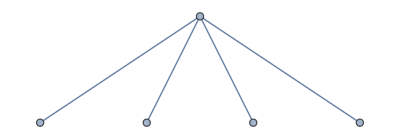
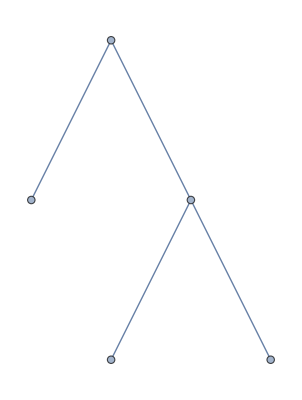
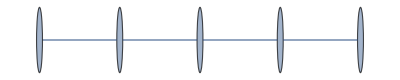
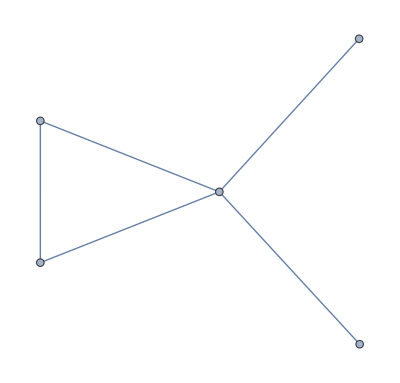
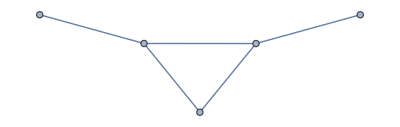
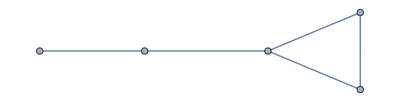
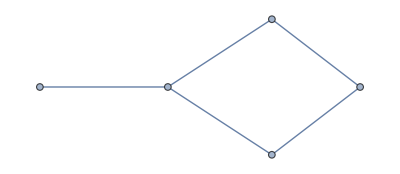
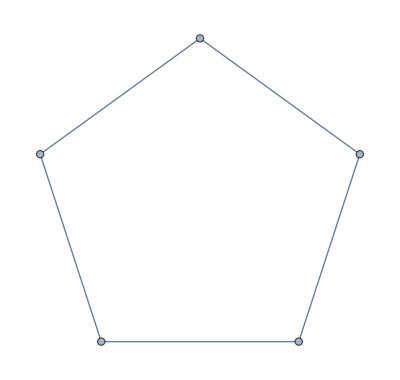
{{-Graphics-,{{1,3,1},{1,2,1,1},{1,1,2,1},{1,1,1,1,1}}},{-Graphics-,{{1,2,1,1},{1,1,2,1},{1,1,1,1,1}}},{-Graphics-,{{1,1,1,1,1}}},{-Graphics-,{{2,2,1},{1,2,2},{2,1,1,1},{1,2,1,1},{1,1,2,1},{1,1,1,2},{1,1,1,1,1}}},{-Graphics-,{{2,1,1,1},{1,2,1,1},{1,1,2,1},{1,1,1,2},{1,1,1,1,1}}},{-Graphics-,{{2,1,1,1},{1,2,1,1},{1,1,2,1},{1,1,1,2},{1,1,1,1,1}}},{-Graphics-,{{2,2,1},{1,2,2},{2,1,1,1},{1,2,1,1},{1,1,2,1},{1,1,1,2},{1,1,1,1,1}}},{-Graphics-,{{2,2,1},{1,2,2},{2,1,1,1},{1,2,1,1},{1,1,2,1},{1,1,1,2},{1,1,1,1,1}}},{-Graphics-,{{2,2,1},{2,1,2},{1,2,2},{2,1,1,1},{1,2,1,1},{1,1,2,1},{1,1,1,2},{1,1,1,1,1}}},{-Graphics-,{{2,2,1},{2,1,2},{1,2,2},{2,1,1,1},{1,2,1,1},{1,1,2,1},{1,1,1,2},{1,1,1,1,1}}},{-Graphics-,{{3,1,1},{1,3,1},{1,1,3},{2,2,1},{2,1,2},{1,2,2},{2,1,1,1},{1,2,1,1},{1,1,2,1},{1,1,1,2},{1,1,1,1,1}}},{-Graphics-,{{2,2,1},{2,1,2},{1,2,2},{2,1,1,1},{1,2,1,1},{1,1,2,1},{1,1,1,2},{1,1,1,1,1}}},{-Graphics-,{{1,3,1},{2,2,1},{2,1,2},{1,2,2},{2,1,1,1},{1,2,1,1},{1,1,2,1},{1,1,1,2},{1,1,1,1,1}}},{-Graphics-,{{3,1,1},{1,3,1},{1,1,3},{2,2,1},{2,1,2},{1,2,2},{2,1,1,1},{1,2,1,1},{1,1,2,1},{1,1,1,2},{1,1,1,1,1}}},{-Graphics-,{{1,3,1},{2,2,1},{2,1,2},{1,2,2},{2,1,1,1},{1,2,1,1},{1,1,2,1},{1,1,1,2},{1,1,1,1,1}}},{-Graphics-,{{2,2,1},{2,1,2},{1,2,2},{2,1,1,1},{1,2,1,1},{1,1,2,1},{1,1,1,2},{1,1,1,1,1}}},{-Graphics-,{{3,2},{2,3},{3,1,1},{1,3,1},{1,1,3},{2,2,1},{2,1,2},{1,2,2},{2,1,1,1},{1,2,1,1},{1,1,2,1},{1,1,1,2},{1,1,1,1,1}}},{-Graphics-,{{3,2},{2,3},{3,1,1},{1,3,1},{1,1,3},{2,2,1},{2,1,2},{1,2,2},{2,1,1,1},{1,2,1,1},{1,1,2,1},{1,1,1,2},{1,1,1,1,1}}},{-Graphics-,{{3,2},{2,3},{3,1,1},{1,3,1},{1,1,3},{2,2,1},{2,1,2},{1,2,2},{2,1,1,1},{1,2,1,1},{1,1,2,1},{1,1,1,2},{1,1,1,1,1}}},{-Graphics-,{{3,2},{2,3},{3,1,1},{1,3,1},{1,1,3},{2,2,1},{2,1,2},{1,2,2},{2,1,1,1},{1,2,1,1},{1,1,2,1},{1,1,1,2},{1,1,1,1,1}}},{-Graphics-,{{4,1},{1,4},{3,2},{2,3},{3,1,1},{1,3,1},{1,1,3},{2,2,1},{2,1,2},{1,2,2},{2,1,1,1},{1,2,1,1},{1,1,2,1},{1,1,1,2},{1,1,1,1,1}}}}

```mathematica
(* Find all graphs in the atlas that are connected with 5 vertices *)
n=5;
atlas5=Select[Range[0,1252],(g=atlas[#];ConnectedGraphQ[g]&&VertexCount[g]==n)&];
(* For each element of atlas5, print Calculate the graph and compute the multiplicity list, and flatten/arrange the list of lists appropriately *)
{G=atlas[#],Flatten[DeleteCases[(MultList[G,#]&/@Range[n]),{}],{1,2}]}&/@atlas5
```

```mathematica
(* Find all graphs in the atlas that are connected with 5 vertices *)
n=5;
atlas5=Select[Range[0,1252],(g=atlas[#];ConnectedGraphQ[g]&&VertexCount[g]==n)&];
(* For each element of atlas5, print Calculate the graph and compute the multiplicity list for SKEW SYMMETRIC MATRICES, and flatten/arrange the list of lists appropriately *)
{G=atlas[#],Flatten[DeleteCases[(MultListSkew[G,#]&/@Range[n]),{}],{1,2}]}&/@atlas5
```

{{-Graphics-,{{1,3,1},{1,1,1,1,1}}},{-Graphics-,{{1,1,1,1,1}}},{-Graphics-,{{1,1,1,1,1}}},{-Graphics-,{{1,1,1,1,1}}},{-Graphics-,{{1,1,1,1,1}}},{-Graphics-,{{1,1,1,1,1}}},{-Graphics-,{{1,1,1,1,1}}},{-Graphics-,{{1,1,1,1,1}}},{-Graphics-,{{1,1,1,1,1}}},{-Graphics-,{{1,1,1,1,1}}},{-Graphics-,{{2,1,2},{1,1,1,1,1}}},{-Graphics-,{{1,1,1,1,1}}},{-Graphics-,{{1,3,1},{2,1,2},{1,1,1,1,1}}},{-Graphics-,{{2,1,2},{1,1,1,1,1}}},{-Graphics-,{{1,3,1},{2,1,2},{1,1,1,1,1}}},{-Graphics-,{{2,1,2},{1,1,1,1,1}}},{-Graphics-,{{2,1,2},{1,1,1,1,1}}},{-Graphics-,{{2,1,2},{1,1,1,1,1}}},{-Graphics-,{{1,3,1},{2,1,2},{1,1,1,1,1}}},{-Graphics-,{{1,3,1},{2,1,2},{1,1,1,1,1}}},{-Graphics-,{{1,3,1},{2,1,2},{1,1,1,1,1}}}}

atlas5

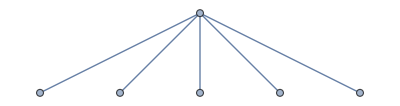
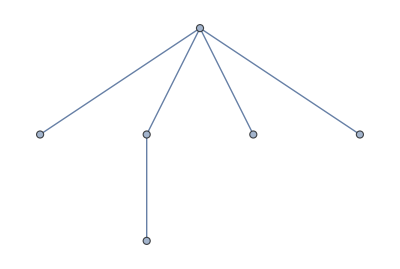
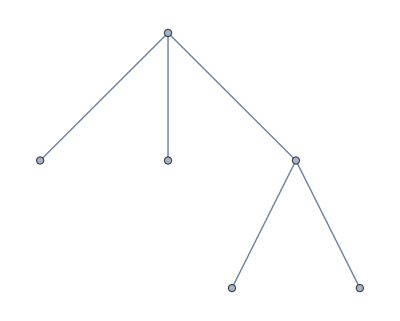
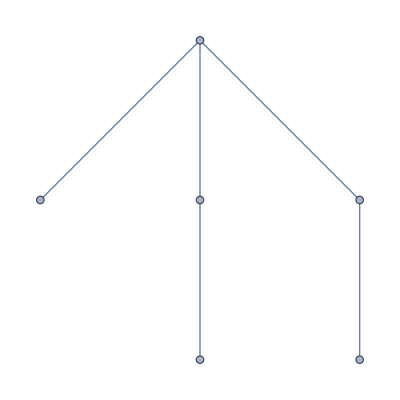
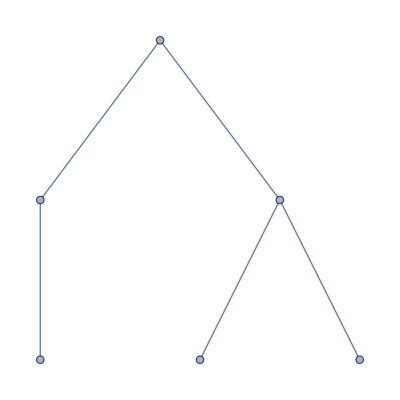
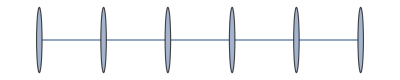
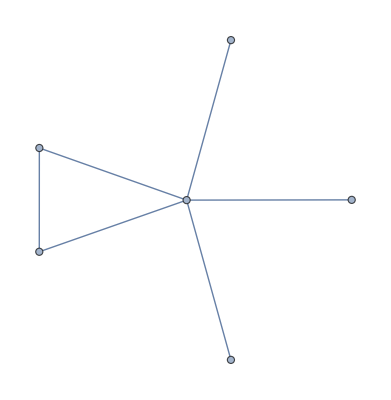
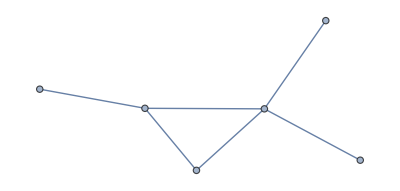
{{-Graphics-,{{1,4,1},{1,3,1,1},{1,1,3,1},{1,2,2,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,1,1}}},{-Graphics-,{{1,3,1,1},{1,1,3,1},{1,2,2,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,1,1}}},{-Graphics-,{{1,2,2,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,1,1}}},{-Graphics-,{{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,1,1}}},{-Graphics-,{{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,1,1}}},{-Graphics-,{{1,1,1,1,1,1}}},{-Graphics-,{{2,3,1},{1,3,2},{1,3,1,1},{1,1,3,1},{2,2,1,1},{2,1,2,1},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{2,2,1,1},{2,1,2,1},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{2,1,2,1},{1,2,1,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{2,2,1,1},{2,1,2,1},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{2,2,1,1},{2,1,2,1},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{2,2,1,1},{2,1,2,1},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{2,2,1,1},{2,1,2,1},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{1,3,1,1},{1,1,3,1},{2,2,1,1},{2,1,2,1},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{2,2,1,1},{2,1,2,1},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{2,2,1,1},{2,1,2,1},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{2,2,1,1},{2,1,2,1},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{2,2,2},{2,2,1,1},{2,1,2,1},{2,1,1,2},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{2,2,1,1},{2,1,2,1},{2,1,1,2},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{2,2,1,1},{2,1,2,1},{2,1,1,2},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{2,3,1},{1,3,2},{2,2,2},{1,3,1,1},{1,1,3,1},{2,2,1,1},{2,1,2,1},{2,1,1,2},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{2,2,2},{2,2,1,1},{2,1,2,1},{2,1,1,2},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{3,2,1},{3,1,2},{2,3,1},{2,1,3},{1,3,2},{1,2,3},{2,2,2},{3,1,1,1},{1,3,1,1},{1,1,3,1},{1,1,1,3},{2,2,1,1},{2,1,2,1},{2,1,1,2},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{2,2,2},{2,2,1,1},{2,1,2,1},{2,1,1,2},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{3,1,1,1},{1,3,1,1},{1,1,3,1},{1,1,1,3},{2,2,1,1},{2,1,2,1},{2,1,1,2},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{2,2,1,1},{2,1,2,1},{2,1,1,2},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{2,3,1},{1,3,2},{2,2,2},{1,3,1,1},{1,1,3,1},{2,2,1,1},{2,1,2,1},{2,1,1,2},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{2,2,1,1},{2,1,2,1},{2,1,1,2},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{2,2,1,1},{2,1,2,1},{2,1,1,2},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{2,2,1,1},{2,1,2,1},{2,1,1,2},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{2,2,2},{1,3,1,1},{1,1,3,1},{2,2,1,1},{2,1,2,1},{2,1,1,2},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{3,2,1},{3,1,2},{2,3,1},{2,1,3},{1,3,2},{1,2,3},{2,2,2},{3,1,1,1},{1,3,1,1},{1,1,3,1},{1,1,1,3},{2,2,1,1},{2,1,2,1},{2,1,1,2},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{2,2,2},{2,2,1,1},{2,1,2,1},{2,1,1,2},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{2,2,2},{2,2,1,1},{2,1,2,1},{2,1,1,2},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{2,3,1},{1,3,2},{2,2,2},{1,3,1,1},{1,1,3,1},{2,2,1,1},{2,1,2,1},{2,1,1,2},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{3,1,1,1},{1,3,1,1},{1,1,3,1},{1,1,1,3},{2,2,1,1},{2,1,2,1},{2,1,1,2},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{3,2,1},{3,1,2},{2,3,1},{2,1,3},{1,3,2},{1,2,3},{2,2,2},{3,1,1,1},{1,3,1,1},{1,1,3,1},{1,1,1,3},{2,2,1,1},{2,1,2,1},{2,1,1,2},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{3,1,1,1},{1,3,1,1},{1,1,3,1},{1,1,1,3},{2,2,1,1},{2,1,2,1},{2,1,1,2},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{2,3,1},{1,3,2},{2,2,2},{1,3,1,1},{1,1,3,1},{2,2,1,1},{2,1,2,1},{2,1,1,2},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{2,2,2},{2,2,1,1},{2,1,2,1},{2,1,1,2},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{2,2,2},{2,2,1,1},{2,1,2,1},{2,1,1,2},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{2,2,2},{1,3,1,1},{1,1,3,1},{2,2,1,1},{2,1,2,1},{2,1,1,2},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{2,2,1,1},{2,1,2,1},{2,1,1,2},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{3,2,1},{3,1,2},{2,3,1},{2,1,3},{1,3,2},{1,2,3},{2,2,2},{3,1,1,1},{1,3,1,1},{1,1,3,1},{1,1,1,3},{2,2,1,1},{2,1,2,1},{2,1,1,2},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{3,2,1},{3,1,2},{2,3,1},{2,1,3},{1,3,2},{1,2,3},{2,2,2},{3,1,1,1},{1,3,1,1},{1,1,3,1},{1,1,1,3},{2,2,1,1},{2,1,2,1},{2,1,1,2},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{3,1,1,1},{1,3,1,1},{1,1,3,1},{1,1,1,3},{2,2,1,1},{2,1,2,1},{2,1,1,2},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{3,2,1},{3,1,2},{2,3,1},{2,1,3},{1,3,2},{1,2,3},{2,2,2},{3,1,1,1},{1,3,1,1},{1,1,3,1},{1,1,1,3},{2,2,1,1},{2,1,2,1},{2,1,1,2},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{3,2,1},{3,1,2},{2,3,1},{2,1,3},{1,3,2},{1,2,3},{2,2,2},{3,1,1,1},{1,3,1,1},{1,1,3,1},{1,1,1,3},{2,2,1,1},{2,1,2,1},{2,1,1,2},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{2,3,1},{1,3,2},{2,2,2},{1,3,1,1},{1,1,3,1},{2,2,1,1},{2,1,2,1},{2,1,1,2},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{1,4,1},{2,3,1},{1,3,2},{2,2,2},{1,3,1,1},{1,1,3,1},{2,2,1,1},{2,1,2,1},{2,1,1,2},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{2,2,2},{2,2,1,1},{2,1,2,1},{2,1,1,2},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{2,2,2},{2,2,1,1},{2,1,2,1},{2,1,1,2},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{2,3,1},{1,3,2},{2,2,2},{1,3,1,1},{1,1,3,1},{2,2,1,1},{2,1,2,1},{2,1,1,2},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{3,2,1},{3,1,2},{2,3,1},{2,1,3},{1,3,2},{1,2,3},{2,2,2},{3,1,1,1},{1,3,1,1},{1,1,3,1},{1,1,1,3},{2,2,1,1},{2,1,2,1},{2,1,1,2},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{3,2,1},{3,1,2},{2,3,1},{2,1,3},{1,3,2},{1,2,3},{2,2,2},{3,1,1,1},{1,3,1,1},{1,1,3,1},{1,1,1,3},{2,2,1,1},{2,1,2,1},{2,1,1,2},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{2,2,2},{2,2,1,1},{2,1,2,1},{2,1,1,2},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{3,2,1},{3,1,2},{2,3,1},{2,1,3},{1,3,2},{1,2,3},{2,2,2},{3,1,1,1},{1,3,1,1},{1,1,3,1},{1,1,1,3},{2,2,1,1},{2,1,2,1},{2,1,1,2},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{3,3},{3,2,1},{3,1,2},{2,3,1},{2,1,3},{1,3,2},{1,2,3},{2,2,2},{3,1,1,1},{1,3,1,1},{1,1,3,1},{1,1,1,3},{2,2,1,1},{2,1,2,1},{2,1,1,2},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{3,2,1},{3,1,2},{2,3,1},{2,1,3},{1,3,2},{1,2,3},{2,2,2},{3,1,1,1},{1,3,1,1},{1,1,3,1},{1,1,1,3},{2,2,1,1},{2,1,2,1},{2,1,1,2},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{3,2,1},{3,1,2},{2,3,1},{2,1,3},{1,3,2},{1,2,3},{2,2,2},{3,1,1,1},{1,3,1,1},{1,1,3,1},{1,1,1,3},{2,2,1,1},{2,1,2,1},{2,1,1,2},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{3,2,1},{3,1,2},{2,3,1},{2,1,3},{1,3,2},{1,2,3},{2,2,2},{3,1,1,1},{1,3,1,1},{1,1,3,1},{1,1,1,3},{2,2,1,1},{2,1,2,1},{2,1,1,2},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{3,2,1},{3,1,2},{2,3,1},{2,1,3},{1,3,2},{1,2,3},{2,2,2},{3,1,1,1},{1,3,1,1},{1,1,3,1},{1,1,1,3},{2,2,1,1},{2,1,2,1},{2,1,1,2},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{3,2,1},{3,1,2},{2,3,1},{2,1,3},{1,3,2},{1,2,3},{2,2,2},{3,1,1,1},{1,3,1,1},{1,1,3,1},{1,1,1,3},{2,2,1,1},{2,1,2,1},{2,1,1,2},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{1,4,1},{2,3,1},{1,3,2},{2,2,2},{1,3,1,1},{1,1,3,1},{2,2,1,1},{2,1,2,1},{2,1,1,2},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{2,3,1},{1,3,2},{2,2,2},{1,3,1,1},{1,1,3,1},{2,2,1,1},{2,1,2,1},{2,1,1,2},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{3,2,1},{3,1,2},{2,3,1},{2,1,3},{1,3,2},{1,2,3},{2,2,2},{3,1,1,1},{1,3,1,1},{1,1,3,1},{1,1,1,3},{2,2,1,1},{2,1,2,1},{2,1,1,2},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{2,2,2},{2,2,1,1},{2,1,2,1},{2,1,1,2},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{4,1,1},{1,4,1},{1,1,4},{3,2,1},{3,1,2},{2,3,1},{2,1,3},{1,3,2},{1,2,3},{2,2,2},{3,1,1,1},{1,3,1,1},{1,1,3,1},{1,1,1,3},{2,2,1,1},{2,1,2,1},{2,1,1,2},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{3,2,1},{3,1,2},{2,3,1},{2,1,3},{1,3,2},{1,2,3},{2,2,2},{3,1,1,1},{1,3,1,1},{1,1,3,1},{1,1,1,3},{2,2,1,1},{2,1,2,1},{2,1,1,2},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{2,2,2},{2,2,1,1},{2,1,2,1},{2,1,1,2},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{3,3},{3,2,1},{3,1,2},{2,3,1},{2,1,3},{1,3,2},{1,2,3},{2,2,2},{3,1,1,1},{1,3,1,1},{1,1,3,1},{1,1,1,3},{2,2,1,1},{2,1,2,1},{2,1,1,2},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{3,2,1},{3,1,2},{2,3,1},{2,1,3},{1,3,2},{1,2,3},{2,2,2},{3,1,1,1},{1,3,1,1},{1,1,3,1},{1,1,1,3},{2,2,1,1},{2,1,2,1},{2,1,1,2},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{3,2,1},{3,1,2},{2,3,1},{2,1,3},{1,3,2},{1,2,3},{2,2,2},{3,1,1,1},{1,3,1,1},{1,1,3,1},{1,1,1,3},{2,2,1,1},{2,1,2,1},{2,1,1,2},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{3,2,1},{3,1,2},{2,3,1},{2,1,3},{1,3,2},{1,2,3},{2,2,2},{3,1,1,1},{1,3,1,1},{1,1,3,1},{1,1,1,3},{2,2,1,1},{2,1,2,1},{2,1,1,2},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{3,2,1},{3,1,2},{2,3,1},{2,1,3},{1,3,2},{1,2,3},{2,2,2},{3,1,1,1},{1,3,1,1},{1,1,3,1},{1,1,1,3},{2,2,1,1},{2,1,2,1},{2,1,1,2},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{3,2,1},{3,1,2},{2,3,1},{2,1,3},{1,3,2},{1,2,3},{2,2,2},{3,1,1,1},{1,3,1,1},{1,1,3,1},{1,1,1,3},{2,2,1,1},{2,1,2,1},{2,1,1,2},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{3,3},{3,2,1},{3,1,2},{2,3,1},{2,1,3},{1,3,2},{1,2,3},{2,2,2},{3,1,1,1},{1,3,1,1},{1,1,3,1},{1,1,1,3},{2,2,1,1},{2,1,2,1},{2,1,1,2},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{3,3},{1,4,1},{3,2,1},{3,1,2},{2,3,1},{2,1,3},{1,3,2},{1,2,3},{2,2,2},{3,1,1,1},{1,3,1,1},{1,1,3,1},{1,1,1,3},{2,2,1,1},{2,1,2,1},{2,1,1,2},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{3,2,1},{3,1,2},{2,3,1},{2,1,3},{1,3,2},{1,2,3},{2,2,2},{3,1,1,1},{1,3,1,1},{1,1,3,1},{1,1,1,3},{2,2,1,1},{2,1,2,1},{2,1,1,2},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{3,2,1},{3,1,2},{2,3,1},{2,1,3},{1,3,2},{1,2,3},{2,2,2},{3,1,1,1},{1,3,1,1},{1,1,3,1},{1,1,1,3},{2,2,1,1},{2,1,2,1},{2,1,1,2},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{3,2,1},{3,1,2},{2,3,1},{2,1,3},{1,3,2},{1,2,3},{2,2,2},{3,1,1,1},{1,3,1,1},{1,1,3,1},{1,1,1,3},{2,2,1,1},{2,1,2,1},{2,1,1,2},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{3,2,1},{3,1,2},{2,3,1},{2,1,3},{1,3,2},{1,2,3},{2,2,2},{3,1,1,1},{1,3,1,1},{1,1,3,1},{1,1,1,3},{2,2,1,1},{2,1,2,1},{2,1,1,2},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{3,3},{3,2,1},{3,1,2},{2,3,1},{2,1,3},{1,3,2},{1,2,3},{2,2,2},{3,1,1,1},{1,3,1,1},{1,1,3,1},{1,1,1,3},{2,2,1,1},{2,1,2,1},{2,1,1,2},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{3,2,1},{3,1,2},{2,3,1},{2,1,3},{1,3,2},{1,2,3},{2,2,2},{3,1,1,1},{1,3,1,1},{1,1,3,1},{1,1,1,3},{2,2,1,1},{2,1,2,1},{2,1,1,2},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{3,2,1},{3,1,2},{2,3,1},{2,1,3},{1,3,2},{1,2,3},{2,2,2},{3,1,1,1},{1,3,1,1},{1,1,3,1},{1,1,1,3},{2,2,1,1},{2,1,2,1},{2,1,1,2},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{3,2,1},{3,1,2},{2,3,1},{2,1,3},{1,3,2},{1,2,3},{2,2,2},{3,1,1,1},{1,3,1,1},{1,1,3,1},{1,1,1,3},{2,2,1,1},{2,1,2,1},{2,1,1,2},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{3,2,1},{3,1,2},{2,3,1},{2,1,3},{1,3,2},{1,2,3},{2,2,2},{3,1,1,1},{1,3,1,1},{1,1,3,1},{1,1,1,3},{2,2,1,1},{2,1,2,1},{2,1,1,2},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{3,3},{3,2,1},{3,1,2},{2,3,1},{2,1,3},{1,3,2},{1,2,3},{2,2,2},{3,1,1,1},{1,3,1,1},{1,1,3,1},{1,1,1,3},{2,2,1,1},{2,1,2,1},{2,1,1,2},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{3,3},{3,2,1},{3,1,2},{2,3,1},{2,1,3},{1,3,2},{1,2,3},{2,2,2},{3,1,1,1},{1,3,1,1},{1,1,3,1},{1,1,1,3},{2,2,1,1},{2,1,2,1},{2,1,1,2},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{3,3},{3,2,1},{3,1,2},{2,3,1},{2,1,3},{1,3,2},{1,2,3},{2,2,2},{3,1,1,1},{1,3,1,1},{1,1,3,1},{1,1,1,3},{2,2,1,1},{2,1,2,1},{2,1,1,2},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{3,3},{1,4,1},{3,2,1},{3,1,2},{2,3,1},{2,1,3},{1,3,2},{1,2,3},{2,2,2},{3,1,1,1},{1,3,1,1},{1,1,3,1},{1,1,1,3},{2,2,1,1},{2,1,2,1},{2,1,1,2},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{4,2},{2,4},{3,3},{4,1,1},{1,4,1},{1,1,4},{3,2,1},{3,1,2},{2,3,1},{2,1,3},{1,3,2},{1,2,3},{2,2,2},{3,1,1,1},{1,3,1,1},{1,1,3,1},{1,1,1,3},{2,2,1,1},{2,1,2,1},{2,1,1,2},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{4,1,1},{1,4,1},{1,1,4},{3,2,1},{3,1,2},{2,3,1},{2,1,3},{1,3,2},{1,2,3},{2,2,2},{3,1,1,1},{1,3,1,1},{1,1,3,1},{1,1,1,3},{2,2,1,1},{2,1,2,1},{2,1,1,2},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{3,3},{3,2,1},{3,1,2},{2,3,1},{2,1,3},{1,3,2},{1,2,3},{2,2,2},{3,1,1,1},{1,3,1,1},{1,1,3,1},{1,1,1,3},{2,2,1,1},{2,1,2,1},{2,1,1,2},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{3,2,1},{3,1,2},{2,3,1},{2,1,3},{1,3,2},{1,2,3},{2,2,2},{3,1,1,1},{1,3,1,1},{1,1,3,1},{1,1,1,3},{2,2,1,1},{2,1,2,1},{2,1,1,2},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{4,2},{2,4},{3,3},{4,1,1},{1,4,1},{1,1,4},{3,2,1},{3,1,2},{2,3,1},{2,1,3},{1,3,2},{1,2,3},{2,2,2},{3,1,1,1},{1,3,1,1},{1,1,3,1},{1,1,1,3},{2,2,1,1},{2,1,2,1},{2,1,1,2},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{4,2},{2,4},{3,3},{4,1,1},{1,4,1},{1,1,4},{3,2,1},{3,1,2},{2,3,1},{2,1,3},{1,3,2},{1,2,3},{2,2,2},{3,1,1,1},{1,3,1,1},{1,1,3,1},{1,1,1,3},{2,2,1,1},{2,1,2,1},{2,1,1,2},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{3,3},{3,2,1},{3,1,2},{2,3,1},{2,1,3},{1,3,2},{1,2,3},{2,2,2},{3,1,1,1},{1,3,1,1},{1,1,3,1},{1,1,1,3},{2,2,1,1},{2,1,2,1},{2,1,1,2},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{3,3},{1,4,1},{3,2,1},{3,1,2},{2,3,1},{2,1,3},{1,3,2},{1,2,3},{2,2,2},{3,1,1,1},{1,3,1,1},{1,1,3,1},{1,1,1,3},{2,2,1,1},{2,1,2,1},{2,1,1,2},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{3,3},{3,2,1},{3,1,2},{2,3,1},{2,1,3},{1,3,2},{1,2,3},{2,2,2},{3,1,1,1},{1,3,1,1},{1,1,3,1},{1,1,1,3},{2,2,1,1},{2,1,2,1},{2,1,1,2},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{4,2},{2,4},{3,3},{4,1,1},{1,4,1},{1,1,4},{3,2,1},{3,1,2},{2,3,1},{2,1,3},{1,3,2},{1,2,3},{2,2,2},{3,1,1,1},{1,3,1,1},{1,1,3,1},{1,1,1,3},{2,2,1,1},{2,1,2,1},{2,1,1,2},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{4,2},{2,4},{3,3},{4,1,1},{1,4,1},{1,1,4},{3,2,1},{3,1,2},{2,3,1},{2,1,3},{1,3,2},{1,2,3},{2,2,2},{3,1,1,1},{1,3,1,1},{1,1,3,1},{1,1,1,3},{2,2,1,1},{2,1,2,1},{2,1,1,2},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{3,3},{1,4,1},{3,2,1},{3,1,2},{2,3,1},{2,1,3},{1,3,2},{1,2,3},{2,2,2},{3,1,1,1},{1,3,1,1},{1,1,3,1},{1,1,1,3},{2,2,1,1},{2,1,2,1},{2,1,1,2},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{3,3},{3,2,1},{3,1,2},{2,3,1},{2,1,3},{1,3,2},{1,2,3},{2,2,2},{3,1,1,1},{1,3,1,1},{1,1,3,1},{1,1,1,3},{2,2,1,1},{2,1,2,1},{2,1,1,2},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{4,2},{2,4},{3,3},{4,1,1},{1,4,1},{1,1,4},{3,2,1},{3,1,2},{2,3,1},{2,1,3},{1,3,2},{1,2,3},{2,2,2},{3,1,1,1},{1,3,1,1},{1,1,3,1},{1,1,1,3},{2,2,1,1},{2,1,2,1},{2,1,1,2},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{4,2},{2,4},{3,3},{4,1,1},{1,4,1},{1,1,4},{3,2,1},{3,1,2},{2,3,1},{2,1,3},{1,3,2},{1,2,3},{2,2,2},{3,1,1,1},{1,3,1,1},{1,1,3,1},{1,1,1,3},{2,2,1,1},{2,1,2,1},{2,1,1,2},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{4,2},{2,4},{3,3},{4,1,1},{1,4,1},{1,1,4},{3,2,1},{3,1,2},{2,3,1},{2,1,3},{1,3,2},{1,2,3},{2,2,2},{3,1,1,1},{1,3,1,1},{1,1,3,1},{1,1,1,3},{2,2,1,1},{2,1,2,1},{2,1,1,2},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{4,2},{2,4},{3,3},{4,1,1},{1,4,1},{1,1,4},{3,2,1},{3,1,2},{2,3,1},{2,1,3},{1,3,2},{1,2,3},{2,2,2},{3,1,1,1},{1,3,1,1},{1,1,3,1},{1,1,1,3},{2,2,1,1},{2,1,2,1},{2,1,1,2},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{4,2},{2,4},{3,3},{4,1,1},{1,4,1},{1,1,4},{3,2,1},{3,1,2},{2,3,1},{2,1,3},{1,3,2},{1,2,3},{2,2,2},{3,1,1,1},{1,3,1,1},{1,1,3,1},{1,1,1,3},{2,2,1,1},{2,1,2,1},{2,1,1,2},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}},{-Graphics-,{{5,1},{1,5},{4,2},{2,4},{3,3},{4,1,1},{1,4,1},{1,1,4},{3,2,1},{3,1,2},{2,3,1},{2,1,3},{1,3,2},{1,2,3},{2,2,2},{3,1,1,1},{1,3,1,1},{1,1,3,1},{1,1,1,3},{2,2,1,1},{2,1,2,1},{2,1,1,2},{1,2,2,1},{1,2,1,2},{1,1,2,2},{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2},{1,1,1,1,1,1}}}}

```mathematica
(* Find all graphs in the atlas that are connected with 6 vertices *)
n=6;
atlas6=Select[Range[0,1252],(g=atlas[#];ConnectedGraphQ[g]&&VertexCount[g]==n)&];
(* For each element of atlas6, print Calculate the graph and compute the multiplicity list, and flatten/arrange the list of lists appropriately *)
{G=atlas[#],Flatten[DeleteCases[(MultList[G,#]&/@Range[n]),{}],{1,2}]}&/@atlas6
```

```mathematica
atlas[187]
```

-Graphics-